```mathematica
vor1[x_,y_,z_]:=Module[{ζ=1.0,Δ=0.5},If[y==0&&z==0&&x==0,0,Δ Tanh[Sqrt[x^2+y^2+z^2]/ζ]*(x+I y)/Sqrt[x^2+y^2+z^2]]]
vor2[x_,y_]:=Module[{ζ=1.0,Δ=0.5},If[y==0&&x==0,0,Δ Tanh[Sqrt[x^2+y^2]/ζ]*(x+I y)/Sqrt[x^2+y^2]]]
di=0.2;
te=Abs@Table[vor1[x,y,z],{z,-10,10,di},{y,-10,10,di},{x,-10,10,di}];
te2=Abs@Table[vor2[x,y],{z,-10,10,di},{y,-10,10,di},{x,-10,10,di}];
```

```mathematica
ListSliceDensityPlot3D[te2,"ZStackedPlanes",ImageSize->{Automatic,800},ColorFunction->"IslandColors",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{600,40},LegendLayout->"Row"],Above],LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[te,ColorFunction->ColorData["RedBlueTones"],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{20,600},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]],{After,Top}],ImageSize->{Automatic,800},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[te2,ColorFunction->ColorData["RedBlueTones"],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{20,600},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]],{After,Top}],ImageSize->{Automatic,800},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
phi=Import["phi0.dat"];
p2=Map[Take[#,{1,4}]&,phi];
ListDensityPlot3D[p2,ImageSize->{Automatic,700},ColorFunction->ColorData["RedBlueTones"],AxesStyle->Directive[Orange,24,FontFamily->"Times New Roman"],AxesLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)/π","\!\(\*SubscriptBox[\(k\), \(y\)]\)/π","\!\(\*SubscriptBox[\(k\), \(z\)]\)/π"},AxesStyle->Directive[Orange,24,FontFamily->"Times New Roman"],ViewPoint->{1.3,-2.4,2.},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{20,530},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"],Opacity[0.6]],{After,Top}]]
ListSliceDensityPlot3D[p2,"XStackedPlanes",ImageSize->{Automatic,800},ColorFunction->"IslandColors",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{600,40},LegendLayout->"Row"],Above],LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"],AxesStyle->Directive[Orange,24,FontFamily->"Times New Roman"],AxesLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)/π","\!\(\*SubscriptBox[\(k\), \(y\)]\)/π","\!\(\*SubscriptBox[\(k\), \(z\)]\)/π"},AxesStyle->Directive[Orange,24,FontFamily->"Times New Roman"]]
```

-Graphics3D-

-Graphics3D-

```mathematica
x1=Import["TIldos.dat"];
p1=BubbleChart[x1,BubbleSizes->{0.01,0.1},BubbleScale->"Diameter",ImageSize->Large,PlotRange->{{0,40},{0,40}},ColorFunction->"Rainbow",LabelStyle->Directive[Large,Bold]]
```

-Graphics-

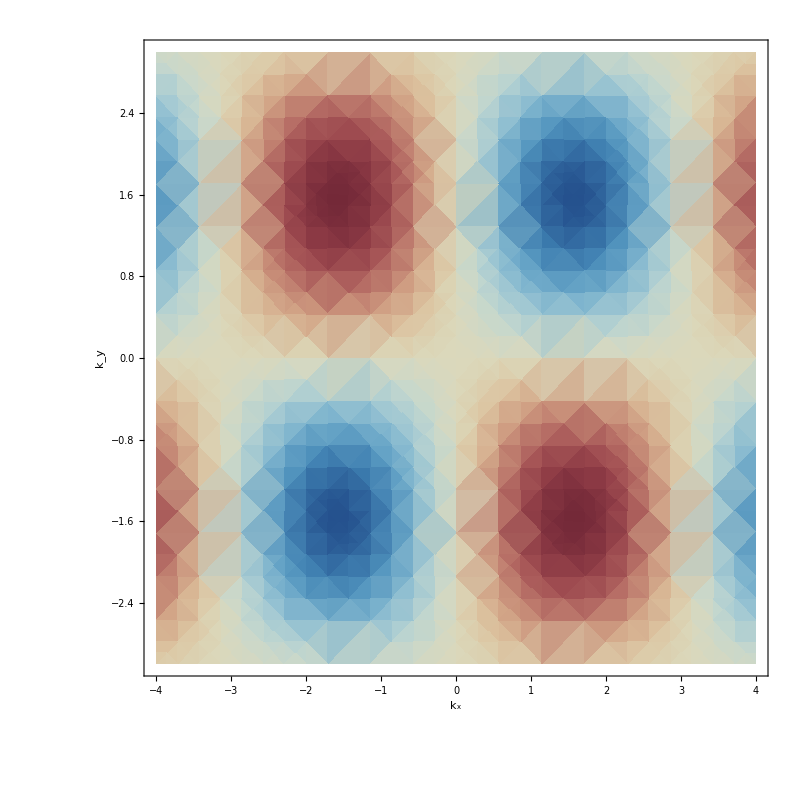

```mathematica
p1=DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3},ColorFunction->ColorData["RedBlueTones"],ImageSize->{800,Automatic},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{750,40},LegendLayout->"Row",LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]],Above],FrameStyle->Directive[Bold,28,FontFamily->"Times"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},PlotRange->{{-4,4},{-3,3}}]
```

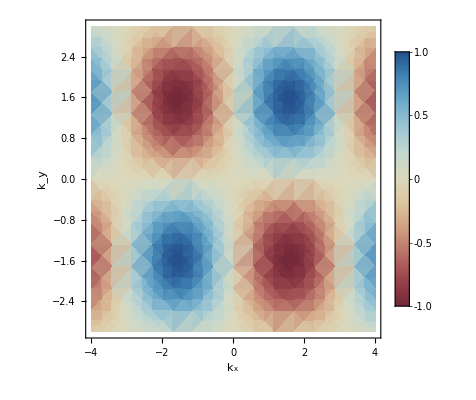

```mathematica
p1=DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3},ColorFunction->ColorData["RedBlueTones"],ImageSize->{Automatic,800},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{40,800},LabelStyle->Directive[Black,FontSize->24,FontFamily->"Times New Roman"]],{After,Top}],FrameStyle->Directive[Bold,28,FontFamily->"Times New Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},PlotRange->{{-4,4},{-3,3}}]
```

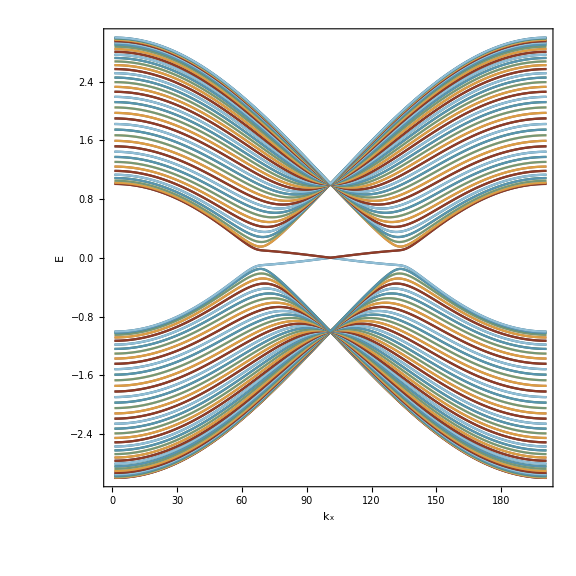

```mathematica
km=Transpose[Import["Km-zigzag.dat"]];
ListLinePlot[km[[2;;]],ImageSize->Large,AspectRatio->1,PlotTheme->"Science",Frame->True,PlotStyle->ColorData[17,"ColorList"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","E"},FrameStyle->Directive[Bold,28,FontFamily->"Times New Roman"],PlotRange->{{0,Length[Transpose@km]-1},{Min[km[[2;;]]],Max[km[[2;;]]]}}]
```

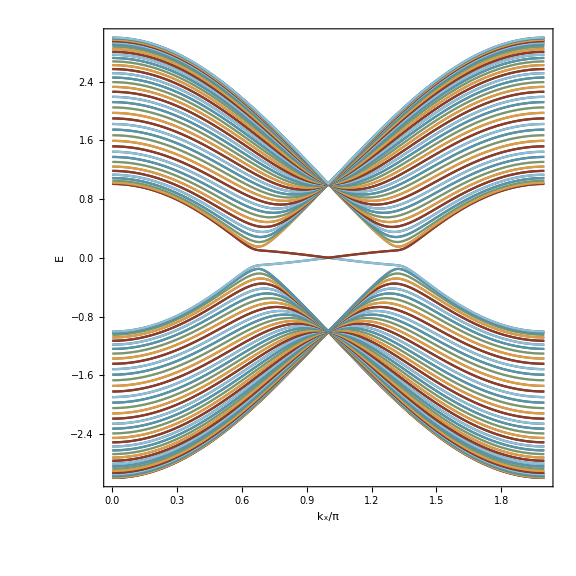

```mathematica
km=Transpose[Import["Km-zigzag.dat"]];
Transpose[{km[[1]],km[[50]]}];
ListLinePlot[Map[Transpose[{km[[1]],#}]&,km[[2;;]]],ImageSize->Large,AspectRatio->1,PlotTheme->"Science",Frame->True,PlotStyle->ColorData[17,"ColorList"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)/π","E"},FrameStyle->Directive[Bold,28,FontFamily->"Times New Roman"],PlotRange->{{Min[km[[1]]],Max[km[[1]]]},{Min[km[[2;;]]],Max[km[[2;;]]]}}]
```

```mathematica
a={{-1,-1},{-1,1},{1,1},{1,-1}};
p1=Graphics[{Lighter@Red,Opacity[0.5],FilledCurve[{Line[a]}]}];
fticks[min_,max_]:=Table[If[EvenQ[i],{i,i,{.03,0},{Black,Thickness[0.004]}},{i,i,{.03,0},{Black,Thickness[0.004]}}],{i,Ceiling[min],Floor[max],1}]
shadowbox[legend_]:=Graphics[{{Gray,Rectangle[{0.05,-0.05},{1.05,0.95}]},{White,EdgeForm[Gray],Rectangle[]},Inset[legend,{0.5,0.5},Center]},ImageSize->80]
p2=Plot[{Sin[kx],-Sin[kx]},{kx,-Pi,Pi},Frame->True,FrameStyle->Directive[24,FontFamily->"Times New Roman"],ImageSize->Large,PlotRange->{{-Pi,Pi},{-1,1}},PlotStyle->Directive[Bold,Thickness[0.005]],FrameTicksStyle->Directive[Black,24],FrameLabel->{Style["k_x",24,FontFamily->"Times New Roman",Black],Style[Rotate["E",-Pi/2],24,FontFamily->"Times New Roman",Black]},PlotLegends->Placed[LineLegend[{Style["Sin x",20,FontFamily->"Times New Roman"]},LegendFunction->shadowbox,LegendLayout->"Column"],{{1.12,0.7},{1,1}}],FrameTicks->fticks];
Show[{p2,p1}]
```

-Graphics-